```mathematica
ClearAll["Global`*"]
NotebookDirectory[] ;
SetDirectory[%];
```

```mathematica
A=1;
u[r_]:=1+A*Tanh[r];
```

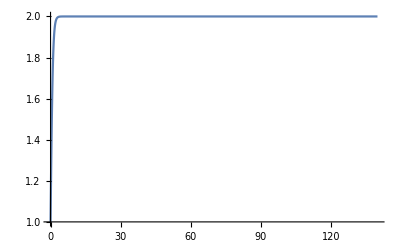

```mathematica
Plot[u[r],{r,0,140},PlotRange->All]
```

```mathematica
du[r_]=D[u[r],r];
```

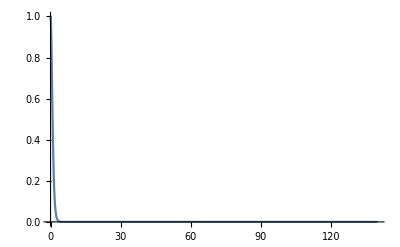

```mathematica
Plot[du[r],{r,0,140},PlotRange->All]
```

```mathematica
gama[r_]:=1+A*Tanh[r];
```

```mathematica
dgama[r_]:=D[gama[r],r];
```

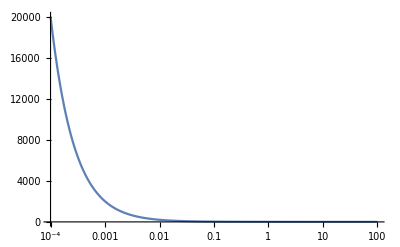

```mathematica
a1[b_]:=b*NIntegrate[((1+gama[r])*u[r])/r^3/.r->√(b^2+z^2),{z,0,∞}];
LogLinearPlot[a1[b],{b,0.0001,100},PlotRange->All]
```

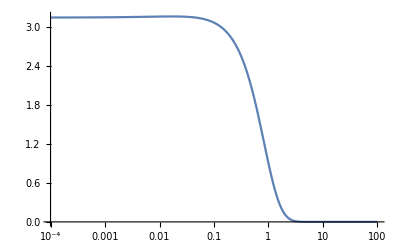

```mathematica
a2[b_]:=b*NIntegrate[((1+gama[r])*du[r])/r^2/.r->√(b^2+z^2),{z,0,Infinity}];
LogLinearPlot[a2[b],{b,0.0001,100},PlotRange->All]
```

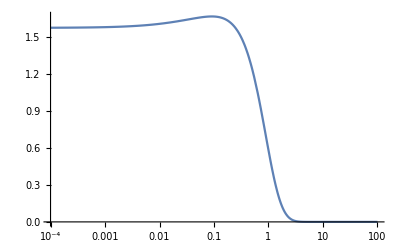

```mathematica
a3[b_]:=b*NIntegrate[(u[r]*dgama[r])/r^2/.r->√(b^2+z^2),{z,0,Infinity}];
LogLinearPlot[a3[b],{b,0.0001,100},PlotRange->All]
```

```mathematica
Ib[b_]:=a1[b]-a2[b]-a3[b];
```

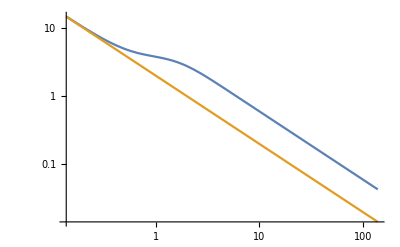

```mathematica
LogLogPlot[{Ib[b],2/b},{b,0,140}]
```

```mathematica
zl=1;
zs=2;
om=0.3;
h0=70;(*km s^-1 Mpc^-1*)
h0c=68;(*km s^-1 Mpc^-1*)
c=3*10^5;(*km s^-1*)
(*Mpc=30.85678*10^18 km*)
(*Msun=1.9891*10^30 kg*)
(*G=6.673*10^-11 m^3 kg^-1 s^-2*)
G=6.673*10^-20*1.9891*10^30;(*km^3 Msun^-1 s^-2*)
M=10^12;(*Msun*)
y=1
```

1

```mathematica
H[t_]:=Sqrt[1-om+om *(1+t)^3];
DA[z_]:=c/h0 1/(1+z)NIntegrate[1/H[t],{t,0,z}];
DA2[z1_,z2_]:=c/h0 1/(1+z2)NIntegrate[1/H[t],{t,z1,z2}];
```

```mathematica
thetaE=√((4G*M)/c^2*1/(30.85678*10^18)*DA2[zl,zs]/(DA[zl]*DA[zs]))
```

6.47201×10^-6

```mathematica
phihMG[x_]:=(4G*M)/c^2*1/(30.85678*10^18)*DA2[zl,zs]/(DA[zl]*DA[zs])NIntegrate[(-(1+r-u[r])*u[r])/(2*r)/.r->√((DA[zl]*x)^2+z^2),{z,0,Infinity}];
```

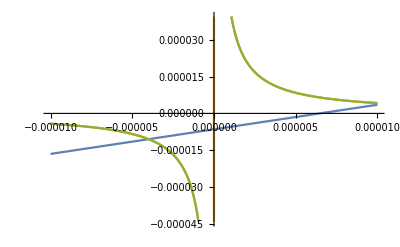

```mathematica
Plot[{theta-y*thetaE,DA2[zl,zs]/DA[zs]*(2G*M)/c^2*1/(30.85678*10^18)*Ib[DA[zl]*theta],(4G*M)/c^2*1/(30.85678*10^18)*DA2[zl,zs]/(DA[zs]DA[zl])*1/theta},{theta,-0.00001,0.00001}]
```

```mathematica
(*NSolve[theta-y*thetaE==DA2[zl,zs]/DA[zs]*(2G*M)/c^2*1/(30.85678*10^18)*Ib[b]/.b->(DA[zl]*theta),theta]*)
```